```mathematica
(* Set Directory to Extract and Save Files to *)
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Environmental Memory Dependence"]
```

C:\Users\physk\OneDrive\Desktop\Environmental Memory Dependence

```mathematica
InitialFilegamma05=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Environmental Memory Dependence\\Entanglement Resonance Ω=ω12=ω34 dependence on γ_0.5.txt"];
```

```mathematica
(* Reformat to only include oscillator 1,2 and 3,4 *)
Reformatfile={InitialFilegamma05[[1]], InitialFilegamma05[[6]]};
```

```mathematica
(* Extract Data Files and save them as a List *)
filestart=1;
Δfilenum=0.5;
numfiles=29;
fileend=filestart + Δfilenum*(numfiles-1);
VarygammaData=Table[ReadList["Entanglement Resonance Ω=ω12=ω34 dependence on γ_"<>ToString[NumberForm[gammavalue, {3, 1}]]<>".txt"], {gammavalue, filestart, fileend,Δfilenum}];
```

```mathematica
(* Include Initial File with gamma = 0.5 *)
gammavalue=Table[gammavalue, {gammavalue, 0.5, 15,0.5}];
VarygammaData=Join[{Reformatfile}, VarygammaData];
```

```mathematica
(* Reformat Data for plotting Density Plots *)
gammaData12=ArrayFlatten[Table[Table[{VarygammaData[[data]][[1]][[point]][[1]], gammavalue[[data]], VarygammaData[[data]][[1]][[point]][[2]]}, {point, 1, Length[VarygammaData[[1]][[1]]]}], {data, 1, 15}], 1];
gammaData34=ArrayFlatten[Table[Table[{VarygammaData[[data]][[2]][[point]][[1]], gammavalue[[data]], VarygammaData[[data]][[2]][[point]][[2]]}, {point, 1, Length[VarygammaData[[1]][[2]]]}], {data, 1, 30}], 1];
```

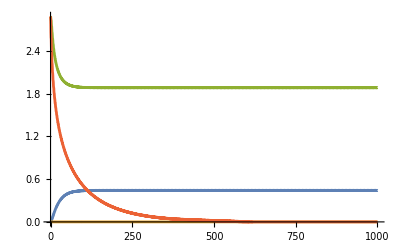

```mathematica
ListLinePlot[{VarygammaData[[1]][[1]], VarygammaData[[8]][[1]], VarygammaData[[1]][[2]], VarygammaData[[30]][[2]]}]
```

```mathematica
(* Gets the saturated values for oscillator pair 1,2 and 3,4 from τ = 600 to 1000 *)
cutoff = Round[0.6*Length[VarygammaData[[1]][[1]]]];
LN12avg = Table[{gammavalue[[data]], Mean[Table[VarygammaData[[data]][[1]][[cutoff;;Length[VarygammaData[[1]][[1]]]]][[points]][[2]], {points, 1, Length[VarygammaData[[1]][[1]]]-cutoff}]]}, {data, 1, 30}];
LN34avg = Table[{gammavalue[[data]], Mean[Table[VarygammaData[[data]][[2]][[cutoff;;Length[VarygammaData[[1]][[1]]]]][[points]][[2]], {points, 1, Length[VarygammaData[[1]][[1]]]-cutoff}]]}, {data, 1, 30}];
```

```mathematica
lm12=LinearModelFit[Table[LN12avg[[1;;8]][[data]], {data, 1, Length[LN12avg[[1;;8]]]}], x, x]
Print["R^2= ", lm12["RSquared"]]
lm34=LinearModelFit[Table[LN34avg[[data]], {data, 1, Length[LN34avg]}], x, x]
Print["R^2= ", lm34["RSquared"]]
```

FittedModel[…]

R^2= 0.985636

FittedModel[…]

R^2= 0.990784

```mathematica
(* Plot Formatting *)
length=350;width=350;
PlotFormat={PlotRange-> {0, 2}, ImageSize->{length, width}, AspectRatio->1, LabelStyle->Directive[Black, 18], AxesLabel->{"γ","𝒩"}, AxesStyle->Directive[Black,18], BaseStyle->{FontFamily->"Latin Modern Roman"}};

height=400;
width=600;
PlotFormat={PlotRange->{0, 2}, ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"γ", "𝒩"}, AxesStyle->Directive[Black,20], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 20], PlotLabel->None, PlotStyle->{Thickness[0.0010]}};

γptsplot=ListPlot[{LN12avg, LN34avg}, PlotStyle->{Directive[Blue, PointSize[0.02]], Directive[Red, PointSize[0.02]]}, PlotRange-> {0, 2}, Evaluate[PlotFormat]];
γ12funcplot=Plot[lm12[x], {x, 0, 4}, PlotStyle->Directive[Blue, Thickness[0.006]], PlotRange-> {0, 2}, Evaluate[PlotFormat]];
γ34funcplot=Plot[lm34[x], {x, 0, 15}, PlotStyle->Directive[Red, Thickness[0.006]], PlotRange-> {0, 2}, Evaluate[PlotFormat]];

EnvironmentalMemoryDependence= Rasterize[Show[γ34funcplot, γ12funcplot, γptsplot]]
```

-Graphics-

Parameters Used
{n, β, η, m, ω, Ω, γ}
{4, 0.3, 0, 1, 2, 2, Varies by 0.5}
{t_start, t_end}
{0, 1000}
But Saturated value is calculated by taking time from {600, 1000}

```mathematica
lm34[x]-lm12[x]
```

1.40484-0.00552108 x

```mathematica
(* Export Graphs to the Set Directory *)
Export["Environmental Memory Dependence.png", EnvironmentalMemoryDependence]
```

Environmental Memory Dependence.png